```mathematica
$Assumptions=ϵ ∈ Reals && ϵ1 ∈ Reals && ϕ ∈ Reals && γl∈ Reals && γr∈ Reals && t0 ∈ Reals
Assumptions->$Assumptions
```

ϵ∈ℝ&&ϵ1∈ℝ&&ϕ∈ℝ&&γl∈ℝ&&γr∈ℝ&&t0∈ℝ

Assumptions→ϵ∈ℝ&&ϵ1∈ℝ&&ϕ∈ℝ&&γl∈ℝ&&γr∈ℝ&&t0∈ℝ

retarded_GF

advanced_GF

product

trace

-((16 ⅇ^(4 ⅈ ϕ) t0^2 γl γr ((-1+ⅇ^(4 ⅈ ϕ)) t0^2+(ϵ-ϵ1)^2) ((-1+ⅇ^(4 ⅈ ϕ)) t0^2-ⅇ^(4 ⅈ ϕ) (ϵ-ϵ1)^2))/((4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+ⅇ^(4 ⅈ ϕ) t0^2 (ⅈ γl+4 ϵ-4 ϵ1) (ⅈ γr+4 ϵ-4 ϵ1)+ⅇ^(4 ⅈ ϕ) (γl-2 ⅈ (ϵ-ϵ1)) (γr-2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2) (4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+ⅇ^(4 ⅈ ϕ) t0^2 (-ⅈ γl+4 ϵ-4 ϵ1) (-ⅈ γr+4 ϵ-4 ϵ1)+ⅇ^(4 ⅈ ϕ) (γl+2 ⅈ (ϵ-ϵ1)) (γr+2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2)))

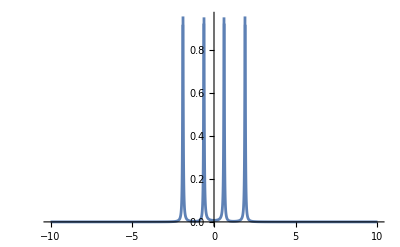

```mathematica
Id =IdentityMatrix[4];
ME= ϵ Id //Simplify;


MH = ({{ϵ1, ts, 0, t}, {t, ϵ1, ts, 0}, {0, t, ϵ1, ts}, {ts, 0, t, ϵ1}});
MΓ= ({{γl, 0, 0, 0}, {0, γr, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});

MΓL= ({{γl, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
MΓR= ({{0, 0, 0, 0}, {0, γr, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});


t=E^(I ϕ) t0;
ts= E^ (-I ϕ) t0;


MGr = ME - MH  + I MΓ/2;
MGa = ME - MH  - I MΓ/2;

(* to see the matrices
*)
(*ME - MH  + I MΓ/2//MatrixForm
ME - MH  - I MΓ/2//MatrixForm*)

retarded_GF

MGr1=MGr/Det[MGr] ;
Inverse[MGr1] //Simplify //MatrixForm          ;
Gr1= Inverse[MGr1] //Simplify;
Gr=1/Det[MGr]  Gr1;
Det[MGr]           ;


advanced_GF

MGa1=MGa/Det[MGa] ;
Inverse[MGa1] //Simplify //MatrixForm       ;
Ga1= Inverse[MGa1] //Simplify;
Ga=1/Det[MGa]  Ga1;
Det[MGa]             ;


product
(*Ga1.MΓR.Gr1.MΓL

Ga1.MΓR.Gr1.MΓL //MatrixForm *)
(* 
Ga1.MΓR //MatrixForm 
Gr1.MΓL //MatrixForm
*)

(*Det[MGa] //Simplify
Det[MGr] //Simplify*)

trace

Tr[Ga1.MΓR.Gr1.MΓL] /Det[MGa]/Det[MGr] //FullSimplify

Clear[ ϵ1, γl, γr, t0, ϕ]
ϵ1=0;
γl=0.1;
γr=0.1;
t0=1;
ϕ=2 Pi/5;

-((16 ⅇ^(4 ⅈ ϕ) t0^2 γl γr ((-1+ⅇ^(4 ⅈ ϕ)) t0^2+(ϵ-ϵ1)^2) ((-1+ⅇ^(4 ⅈ ϕ)) t0^2-ⅇ^(4 ⅈ ϕ) (ϵ-ϵ1)^2))/((4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+ⅇ^(4 ⅈ ϕ) t0^2 (ⅈ γl+4 ϵ-4 ϵ1) (ⅈ γr+4 ϵ-4 ϵ1)+ⅇ^(4 ⅈ ϕ) (γl-2 ⅈ (ϵ-ϵ1)) (γr-2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2) (4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+ⅇ^(4 ⅈ ϕ) t0^2 (-ⅈ γl+4 ϵ-4 ϵ1) (-ⅈ γr+4 ϵ-4 ϵ1)+ⅇ^(4 ⅈ ϕ) (γl+2 ⅈ (ϵ-ϵ1)) (γr+2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2)));

trans[ϵ_]=Tr[Ga1.MΓR.Gr1.MΓL] /Det[MGa]/Det[MGr];
Plot[Re@trans[e], {e, -10. ,10. }, PlotRange->All]
```